1-(7916 t)/3003+(57968 t^2)/15015-(423872 t^3)/135135+(190208 t^4)/135135-(44032 t^5)/135135+(4096 t^6)/135135

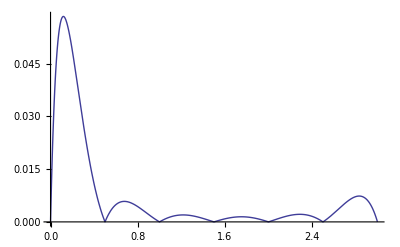

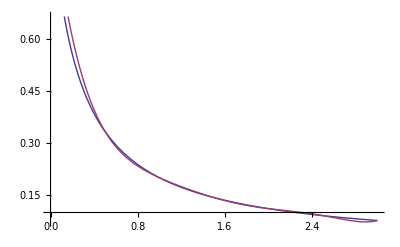

```mathematica
n = 6;
f[t_] := 1 / (1 + 4t);
Do[x[k] = k/2, 
{k, 0, n}];
Do[diff[k, 1] = f[x[k]], 
{k, 0, n}];
Do[
Do[diff[k, j] = (diff[k + 1, j - 1] - diff[k, j - 1] )/ (x[k + j - 1] - x[k]),
 {k, 0, n + 1 - j}],
{j, 2, n + 1}];
P[t_] := 
(s = 0; w = 1;
Do[(s += diff[0, k] * w; w *= t - x[k - 1]), {k, 1, n + 1}];
s);
a = Expand[P[t]]
Plot[Abs[f[t]-a],{t,0,3}, PlotRange -> All]
Plot[{f[t], P[t]}, {t, 0, 3}]
```

1-t+t^2/2-2 t^3+(5 t^3)/ⅇ+(3 t^4)/2-(4 t^4)/ⅇ

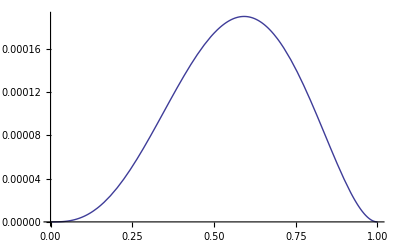

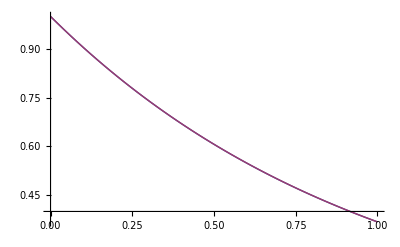

```mathematica
n = 4;
f[t_] := E ^ (-t);
Do[x[k] = 0, 
{k, 0, 2}];
Do[x[k] = 1,
{k, 3, n}];
Do[diff[k, 1] = f[x[k]], 
{k, 0, n}];
Do[
Do[If[x[k]== x[k + j - 1],
diff[k, j] = Derivative[j-1][f][x[k]]/ Factorial[j-1],
diff[k, j] = (diff[k + 1, j - 1] - diff[k, j - 1] )/ (x[k + j - 1] - x[k])],
 {k, 0, n + 1 - j}],
{j, 2, n + 1}];
P[t_] := 
(s = 0; w = 1;
Do[(s += diff[0, k] * w; w *= t - x[k - 1]), {k, 1, n + 1}];
s);
a = Expand[P[t]]
Plot[Abs[f[t]-a],{t,0,1}, PlotRange -> All]
Plot[{f[t], P[t]}, {t, 0, 1}]
(* for checking -> Expand[InterpolatingPolynomial[{{0,1,-1, 1}, {1, 1/E,-1/E}}, x]] *)
```